## Мухамадиев Владимир

# Задание 10

## Загрузка и предварительная обработка

```mathematica
(*Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]*)
```

```mathematica
Needs["IGraphM`"]
```

IGraph/M 0.4 (April 2, 2020)
Evaluate IGDocumentation[] to get started.

```mathematica
g=ExampleData[{"NetworkGraph","DolphinSocialNetwork"}];
```

```mathematica
data=Import[FileNameJoin[{NotebookDirectory[],"data.m"}]];
```

## 1. Спектральные методы выделения сообществ

### По матрице Лапласа

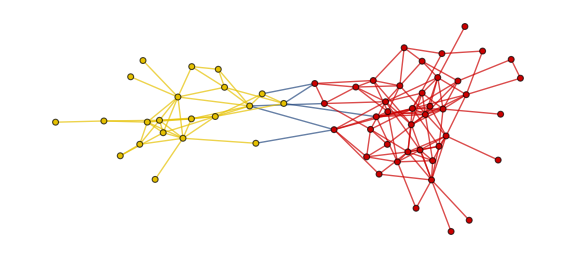

```mathematica
HighlightGraph[g,Subgraph[g,#]&/@With[{data={VertexList[g],Sign[Eigenvectors[N[KirchhoffMatrix[g]]]⟦-2⟧]}ᵀ},{Cases[data,{_,1}]ᵀ⟦1⟧,Cases[data,{_,-1}]ᵀ⟦1⟧}],ImageSize->Large]
```

### По матрице модулярности

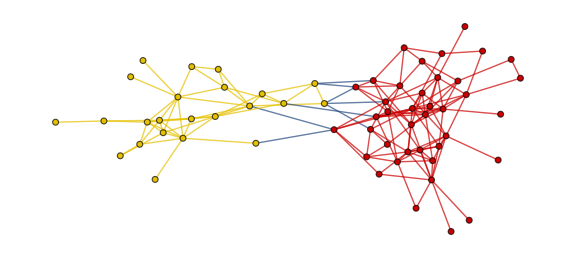

```mathematica
HighlightGraph[g,Subgraph[g,#]&/@IGCommunitiesLeadingEigenvector[g,"ClusterCount"->2]["Communities"],ImageSize->Large]
```

## 2. Label propagation

### 10 запусков

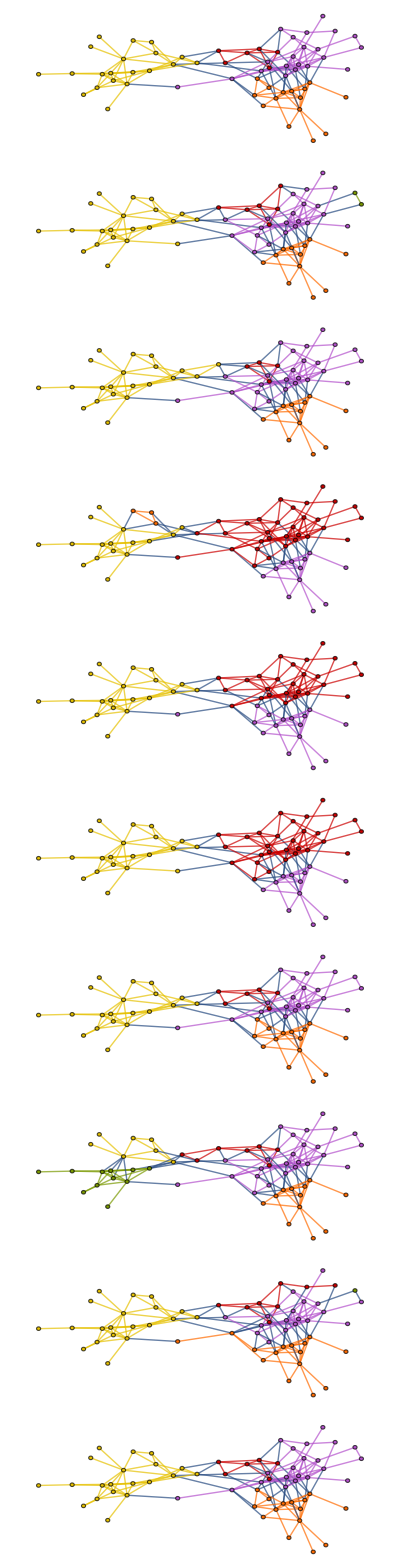

```mathematica
Table[HighlightGraph[g,Subgraph[g,#]&/@IGCommunitiesLabelPropagation[g]["Communities"],ImageSize->Large],{i,1,10}]//TableForm
```

## 3. Тестирование алгоритмов на блочно-стохастических сетях

### Leading Eigenvector

```mathematica
F1[pin_,pout_,n_]:=Module[{graph=IGStochasticBlockModelGame[{{pin,pout},{pout,pin}},{n,n}],μ=pout/(pin+pout),pd={Table[i,{i,1,n}],Table[i,{i,n+1,2n}]},fd={}},fd=IGCommunitiesLeadingEigenvector[graph,"ClusterCount"->2]["Communities"];If[Length[fd]==1,{μ,0.5},{μ,N[(2n-Length[Intersection[pd⟦1⟧,fd⟦2⟧]]-Length[Intersection[pd⟦2⟧,fd⟦1⟧]])/(2n)]}]]
```

#### Среднее по 100 запускам

```mathematica
d1=data⟦1⟧;(*d1=Table[Mean[Table[F1[0.3,p,50],{j,1,100}]],{p,0,0.3,0.01}];*)
```

### Edge Betweenness

```mathematica
F2[pin_,pout_,n_]:=Module[{graph=IGStochasticBlockModelGame[{{pin,pout},{pout,pin}},{n,n}],μ=pout/(pin+pout),pd={Table[i,{i,1,n}],Table[i,{i,n+1,2n}]},fd={}},fd=IGCommunitiesEdgeBetweenness[graph,"ClusterCount"->2]["Communities"];{μ,N[(2n-Length[Intersection[pd⟦1⟧,fd⟦2⟧]]-Length[Intersection[pd⟦2⟧,fd⟦1⟧]])/(2n)]}]
```

#### Среднее по 100 запускам

```mathematica
d2=data⟦2⟧;(*d2=Table[Mean[Table[F2[0.3,p,50],{j,1,100}]],{p,0,0.3,0.01}];*)
```

### Walktrap

```mathematica
F3[pin_,pout_,n_]:=Module[{graph=IGStochasticBlockModelGame[{{pin,pout},{pout,pin}},{n,n}],μ=pout/(pin+pout),pd={Table[i,{i,1,n}],Table[i,{i,n+1,2n}]},fd={}},fd=IGCommunitiesWalktrap[graph,"ClusterCount"->2]["Communities"];{μ,N[(2n-Length[Intersection[pd⟦1⟧,fd⟦2⟧]]-Length[Intersection[pd⟦2⟧,fd⟦1⟧]])/(2n)]}]
```

#### Среднее по 100 запускам

```mathematica
d3=data⟦3⟧;(*d3=Table[Mean[Table[F3[0.3,p,50],{j,1,100}]],{p,0,0.3,0.01}];*)
```

### График

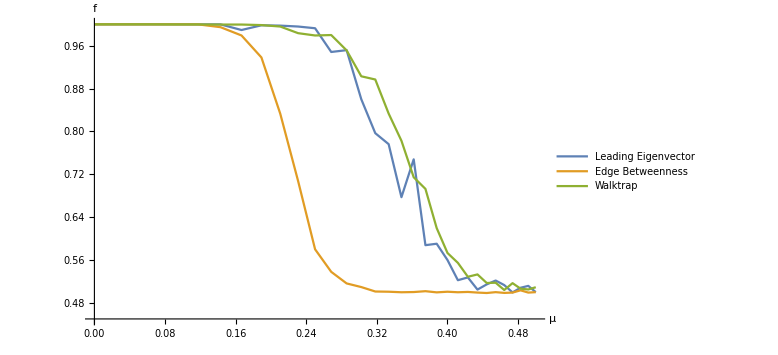

```mathematica
ListLinePlot[{d1,d2,d3},PlotRange->{{0,0.5},{0.45,1}},PlotLegends->Placed[{"Leading Eigenvector","Edge Betweenness","Walktrap"},Below],AxesLabel->{"μ","f"},ImageSize->Large]
```

## 4. Перколяция k-клик

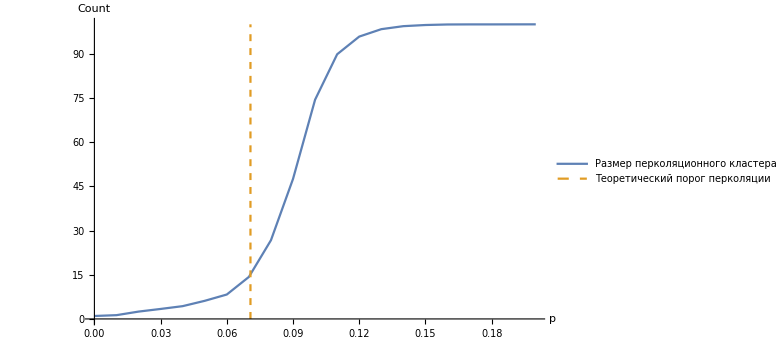

```mathematica
ListLinePlot[{Table[{p,N[Mean[Table[Max[Map[Length,FindGraphCommunities[IGErdosRenyiGameGNP[100,p],Method->"CliquePercolation"]]],{i,1,100}]]]},{p,0,0.2,0.01}],{{N[1/(√(2 100))],0},{N[1/(√(2 100))],100}}},PlotStyle->{Automatic,Dashed},PlotLegends->Placed[{"Размер перколяционного кластера" ,"Теоретический порог перколяции"},Below],AxesLabel->{"p","Count"},ImageSize->Large]
```